```mathematica
k =1.38064852*10^(−23)
m = 1.6726219×10^(-27)
hbar = 1.0545718*10^(−34)
c = 299792458
ρc=1000*1.87*10^(-29)
Simplify[ρc/(m 0.244((k 2.73)/(hbar c))^3)]
```

1.38065×10^-23

1.67262×10^-27

1.05457×10^-34

299792458

1.87×10^-26

2.704×10^-8

```mathematica
Simplify[(ρc*(10^20))/(m 0.244((k 2.73*10^5)/(hbar c))^3)]
```

2.704×10^-23

```mathematica
(10^5)^4
```

100000000000000000000

```mathematica
8.9/(63.5*1.6726219*10^(-24))
```

8.37951×10^22

```mathematica
(10^9)*(8.37951*0.001*10^22)*2*10^(-24)
```

167590.

```mathematica
Sqrt[2*(1.60218*10^(-12) *1.675*10^(-27))]
```

7.32619×10^-20

```mathematica
E^(I*150*π/180)
```

ⅇ^((5 ⅈ π)/6)

```mathematica
(1.05*10^-34)/(7.326*10^-20)
```

1.43325×10^-15

```mathematica
E^(I 5)*E^(-I 4)
E^(I(5-4))
E^(I(4-5))
```

ⅇ^ⅈ

ⅇ^ⅈ

ⅇ^-ⅈ

```mathematica
E^(I*(-30)*π/180-I 150*π/180)
E^(I*150*π/180-I(-30)*π/180)
```

-1

-1

```mathematica
const=hbar^2/(1.60218*10^(-12) *1.675*10^(-27))
```

4.14406×10^-30

5.18008×10^-31

```mathematica
Integrate[
(1+6*Cos[θ]+9*Cos[θ]^2)Sin[θ], {θ, 0, π}]
```

```mathematica
2π*const
```

2.60379×10^-29

```mathematica
(11 π)/2*const
```

8.95053×10^-30

```mathematica
Solve[{p0^2==p1^2-2 m U0,p0/p1==r},{ p1, r}]
```

{{p1→-√(p0^2+2 m U0),r→-p0/(√(p0^2+2 m U0))},{p1→√(p0^2+2 m U0),r→p0/(√(p0^2+2 m U0))}}

```mathematica
Simplify[Solve[{d/x==Sin[α], d/y==Sin[β]}, {d, x}]]
```

{{d→b Cos[α]-R Sin[α],x→-R+b Cot[α]}}

```mathematica
Simplify[Solve[(π-α-β)+θ==π, θ]]
```

{{θ→α+β}}

```mathematica
theta=2ArcSin[b/R]-2 ArcSin[c b / R];
dthetadb=Simplify[D[theta, b]]
```

2/(√(1-b^2/R^2) R)-(2 c)/(√(1-(b^2 c^2)/R^2) R)

```mathematica
phidot =b Sqrt[2 m En]/(m r^2)
rdot = Sqrt[2 (En-U)/ m-r^2 phidot^2 ]
Simplify[phidot/rdot]
```

(√2 b √(En m))/(m r^2)

√(-(2 b^2 En)/(m r^2)+(2 (En-U))/m)

(b En)/(√(En m) r^2 √((-b^2 En+r^2 (En-U))/(m r^2)))

```mathematica
Integrate[(b/r)/Sqrt[r^2-b^2-ge], {r, Sqrt[b^2+ge], Infinity}]
```

ConditionalExpression[(b π)/(2 √(b^2+ge)),b∈Reals&&ge==Re[ge]&&(b+√-ge<0||b>√-ge||Re[ge]>0)]

```mathematica
Solve[{En==γ/r^2+b^2 En/r^2}, r]
```

{{r→-(√(b^2 En+γ))/(√En)},{r→(√(b^2 En+γ))/(√En)}}

```mathematica
Solve[θ==π-(b π)/Sqrt[b^2 +ge], b]
```

{{b→-(ⅈ √ge (π-θ))/(√θ √(-2 π+θ))},{b→(ⅈ √ge (π-θ))/(√θ √(-2 π+θ))}}

```mathematica
Simplify[D[Sqrt[ge/θ](π-θ)/Sqrt[θ-2 π ], θ]]
```

(π^2 √(ge/θ))/(θ (-2 π+θ)^(3/2))

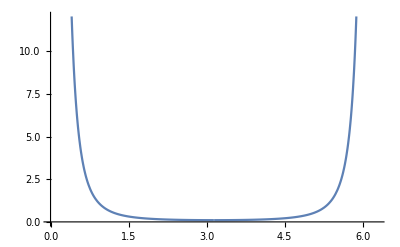

```mathematica
Plot[(π^2(π-θ))/(θ^2(2 π-θ)^2 Sin[θ]), {θ, 0, π 2}]
```